```mathematica
<<peeters`;
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

Solve the simultaneous equations:

x | i cos(θ) + e^(i θ) | = x sin(θ) + 5
| x e^(i θ) - 5| = 2

```mathematica
ClearAll[equations]
equations ={(x Exp[I t] - 5)(x Exp[-I t] - 5) == 4, x^2 ( I Cos[t] + Exp[I t])(-I Cos[t] + Exp[-I t]) == (x Sin[t] + 5 )^2} // FullSimplify
```

{21+x^2==10 x Cos[t],1/2 x^2 (3+Cos[2 t]+2 Sin[2 t])==(5+x Sin[t])^2}

```mathematica
ClearAll[solutions, valid, crit]
solutions = {x,t} /. (NSolve[equations, {x,t}])
crit[{x_, y_}] := (x ∈ Reals && y ∈ Reals && x > 0 && y > 0) ;
valid = Select[solutions /. C[1] -> 0, crit] // First
```

{{-3.43273,ConditionalExpression[1. (2.84056+6.28319 C[1]), C[1]∈ℤ]},{3.43273,ConditionalExpression[1. (-0.301032+6.28319 C[1]), C[1]∈ℤ]},{-4.12018,ConditionalExpression[1. (-2.74325+6.28319 C[1]), C[1]∈ℤ]},{4.12018,ConditionalExpression[1. (0.398344+6.28319 C[1]), C[1]∈ℤ]},{-4.70348+5.33878 ⅈ,ConditionalExpression[1. ((2.23748-0.387751 ⅈ)+6.28319 C[1]), C[1]∈ℤ]},{4.70348-5.33878 ⅈ,ConditionalExpression[1. ((-0.904114-0.387751 ⅈ)+6.28319 C[1]), C[1]∈ℤ]},{-4.70348-5.33878 ⅈ,ConditionalExpression[1. ((2.23748+0.387751 ⅈ)+6.28319 C[1]), C[1]∈ℤ]},{4.70348+5.33878 ⅈ,ConditionalExpression[1. ((-0.904114+0.387751 ⅈ)+6.28319 C[1]), C[1]∈ℤ]}}

{4.12018,0.398344}

Picked out the solution with x > 0 and real and t real > 0 and C[1] = 0

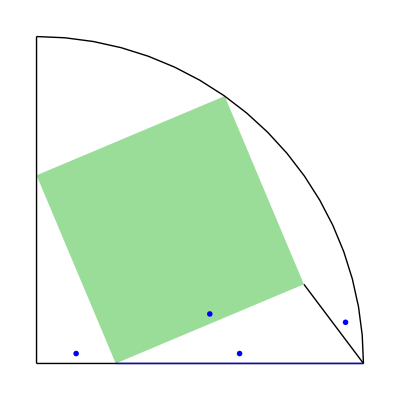

```mathematica
ClearAll[fs, n2s, squareInCircleFig1]
fs = Style[#, FontSize-> 16] &;
n2s := ToString[N[IntegerPart[#*100]/100]] &;

squareInCircleFig1 = Module[{p,q,y,s, o, r, x, t},
{x,t} = valid;
o = {0,0};
y = x Sin[t];
s = I x Cos[t];
p = y + x Exp[I t];
q = s + x Exp[I t];
r = y + 5;
Graphics[ {
Opacity[0.4],
Green// Darker,
Polygon[ {s// ReIm, {y,0}, p // ReIm, q // ReIm}],
Opacity[1],
Black,
Thick,
Circle[o, {r,r},{0, Pi/2}],
Line[{o, {r,0}}],
Line[{o, {0, r}}],
Line[{p//ReIm, {r,0}}],
Blue,
Line[{{y,0}, {r,0}}],
Text[(x// n2s)// MaTeX , {y,0.2} +(( x Exp[I t]/2)// ReIm)] ,
Text["2" // MaTeX , 0.52((p // ReIm) + {r,0})],
Text["5"// MaTeX , {y + 2.5,0.2}  ],
Text[(y // n2s)// MaTeX , {y/2,0.2}  ]
}
]
]
```

## Sofia' s clever way using only Pythagoras:

```mathematica
ClearAll[x,s,y, solutions, valid, crit, system]
system = { x^2 == s^2 + y^2, (5-s)^2 + y^2 == 4, (s + y)^2 + s^2 == (y + 5)^2};
crit[{x_, s_, y_}] := (x ∈ Reals && x > 0 && s ∈ Reals && s > 0 && y ∈ Reals && y > 0) ;
solutions = {x,s,y} /.NSolve[system, {x,s,y}]
valid = Select[solutions /. C[1] -> 0, crit] [[1,1]]
```

{{-4.70348-5.33878 ⅈ,1.46202+5.02217 ⅈ,-5.29018-3.35874 ⅈ},{4.70348+5.33878 ⅈ,1.46202+5.02217 ⅈ,-5.29018-3.35874 ⅈ},{-4.70348+5.33878 ⅈ,1.46202-5.02217 ⅈ,-5.29018+3.35874 ⅈ},{4.70348-5.33878 ⅈ,1.46202-5.02217 ⅈ,-5.29018+3.35874 ⅈ},{-4.12018,3.79759,1.59819},{4.12018,3.79759,1.59819},{-3.43273,3.27836,-1.01783},{3.43273,3.27836,-1.01783}}

4.12018

```mathematica
peeters`setGitDir[ "../project/figures/blogit" ] 
peeters`exportForLatex["squareInCircleFig1", squareInCircleFig1]
```

/Users/pjoot/project/figures/blogit

{squareInCircleFig1.eps,squareInCircleFig1pn.png}